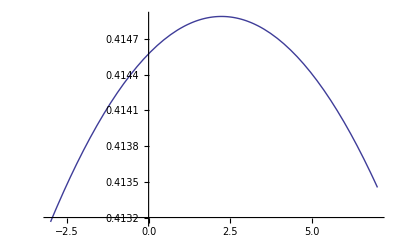

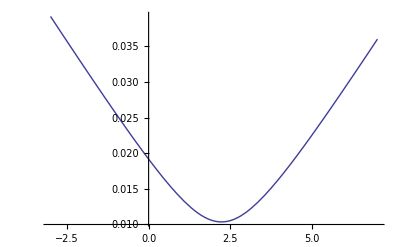

```mathematica
(*Transform pixels to q-space for oriented sample in LAXS setup with motor rotation*)
pz=400;(*vertical pixel position with respect to the beam center*)
pr=10;(*horizontal pixel position with respect to the beam center*)
S=365.1;(*S-distance in mm*)
λ=1.1775;(*wavelength in Angstrom*)
pixel=0.07113;(*pixel size in mm*)
X=pr*pixel;Z=pz*pixel;R=Sqrt[X^2+Z^2];
θ=1/2 ArcTan[R/S];ϕ=ArcTan[Z/X];q=(4π Sin[θ])/λ;
qz[ω_]:=(4π Sin[θ])/λ(Cos[θ]Cos[ω Degree]Sin[ϕ]+Sin[θ]Sin[ω Degree]);
qr[ω_]:=Sqrt[q^2-qz[ω]^2];
Plot[qz[ω],{ω,-3,7}]
Plot[qr[ω],{ω,-3,7}]
```

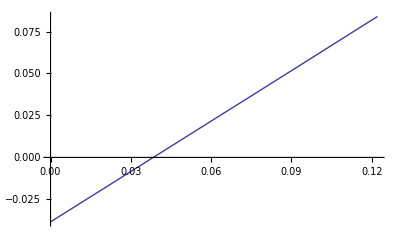

```mathematica
y=2.2Degree;
Plot[Tan[x-y],{x,0Degree,7Degree}]
```